# Doble péndulo

## Solución numérica del doble péndulo

El doble péndulo es un ejemplo de sistema mecánico que pone en evidencia la complejidad que pueden generar este tipo de sistemas de construcción simple. Este sistema en su forma más simple está formado por dos masas colgando de cuerdas de masa despreciable y sin fricción, donde las masas están sujetas a la acción de la gravedad. Se desea describir el movimiento de ambas masas.

No es posible obtener la solución en términos de funciones elementales para este par de ecuaciones diferenciales, lo que pone en evidencia la naturaleza caótica del sistema. A la hora de resolver este tipo de sistemas se suelen utilizar métodos numéricos.

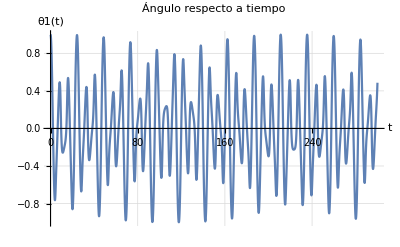

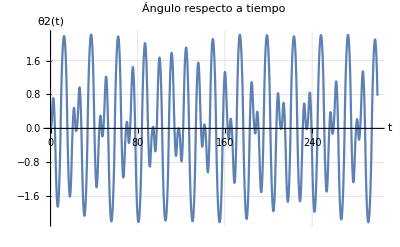

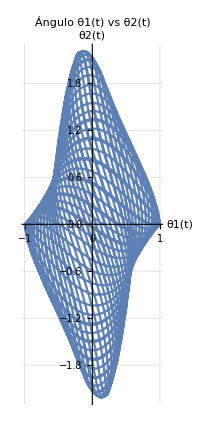

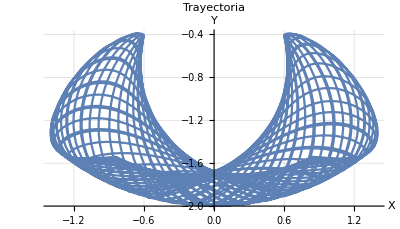

-Graphics3D-

```mathematica
(* Parámetros *)
tMax =300;
With[
{
m1=10.0,m2=5,
l=20.0,g=9.81
},
(* Solución numérica *)sol = NDSolve[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40
]
];

(* Gráficas *)
SetOptions[{Plot,ParametricPlot,ParametricPlot3D},BaseStyle->{FontSize->13}];
Plot[Evaluate[θ1[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ1(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
Plot[Evaluate[θ2[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.sol],{t,0,tMax},AxesLabel->{Style["θ1(t)", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo θ1(t) vs θ2(t)", 15]]
ParametricPlot[Evaluate[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol],{t,0,tMax},AxesLabel->{Style["X", 15], Style["Y", 15]},PlotLabel->Style["Trayectoria", 15], GridLines->Automatic]

ParametricPlot3D[{Evaluate[{θ1[t],θ1'[t], θ1''[t]}/.sol],Evaluate[{θ2[t],θ2'[t], θ2''[t]}/.sol]},{t,0,0.6*tMax},PlotRange->All,AxesLabel->{Style["θ(t)", 15], Style["θ'(t)", 15],Style["θ''(t)", 15]},PlotLabel->Style["Órbitas", 15],
PlotLegends->SwatchLegend[{"Masa 1","Masa 2"}, LegendFunction->"Frame"]
]
```

Visualización de dinámica

```mathematica
Mass1Position[t_,solution_]:=Block[{θ1},{Sin[θ1[t]],-Cos[θ1[t]]}/.First[solution]];
Mass2Position[t_,solution_]:=Block[{θ1,θ2},{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.First[solution]];
DynamicModule[{plt1,plt2},
Manipulate[
plt1 = ParametricPlot[Mass2Position[t,sol],{t,0,tm},Axes->False,PlotRange->{{-2,2},{-2,0}},ImageSize->500,PerformanceGoal->"Quality"];
plt2 = Graphics[
{
Thick,Line[{{0,0},Mass1Position[tm,sol]}],
Thick,Line[{Mass1Position[tm,sol],Mass2Position[tm,sol]}],
EdgeForm[Thick],Red,Disk[Mass1Position[tm,sol],0.15],
EdgeForm[Thick],ColorData["WebSafe"]["#3399FF"],Disk[Mass2Position[tm,sol],0.15],
Black,Text["m_1",Mass1Position[tm,sol]],
Black,Text["m_2",Mass2Position[tm,sol]]
},
PlotRange->{{-2,2},{-2,0}},
ImageSize->500
];
Show[{plt1,plt2}]
,
{{tm,0.01,"Tiempo"},0.01,200,AnimationRate->3,Appearance->"Open"},
TrackedSymbols:>{tm}
]
]
```

## Fractal de doble péndulo

La naturaleza caótica del doble péndulo se puede poner en evidencia creando un mapeo dependiente de las condiciones iniciales en el cual se grafíca si al empezar con unas condiciones iniciales θ_(1i) y θ_(2i) se cumple determinado evento. Este evento puede ser por ejemplo que el segundo péndulo de una vuelta, es decir que θ_2 llegue a tener un valor de π. El mapeo resultante tiene una estructura fractal.

```mathematica
DPFrac[θ1i_,θ2i_,tmax_]:=Module[{m1=10.0,m2=10,l=20.0,g=9.81, sol,max},sol = NDSolveValue[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == θ1i, θ2[0] == θ2i, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tmax}
];
max = FindMaximum[{sol[[2]][t],0 ≤ t ≤ tmax},t];
Return[If[max[[1]] ≥  π, t /. max [[2]], -1]];
]
Dynamic[θ1i]
Dynamic[θ2i]
DensityPlot[DPFrac[θ1i,θ2i,500],{θ1i,-π,π},{θ2i,-π,π},ColorFunction->"SunsetColors",PlotPoints->50]
```